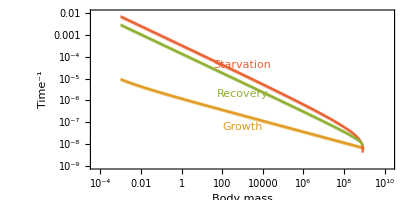

```mathematica
RatePlot=Show[{
Error=0.2;
LogLogPlot[{
Growth,
Growth*(1+Error),
Growth*(1-Error)},{M,0.001,10^9},PlotStyle->{ColorData[97,2],Transparent,Transparent},Filling->{2->{3}},FillingStyle->Directive[{ColorData[97,2],Opacity[0.5]}],
Frame->True,FrameLabel->{"Body mass","Time^-1"},PlotRange->{10^-9,10^-2}],
LogLogPlot[{
Starvation,
Starvation*(1+Error),
Starvation*(1-Error)},{M,0.001,10^9},PlotStyle->{ColorData[97,4],Transparent,Transparent},Filling->{2->{3}},FillingStyle->Directive[{ColorData[97,4],Opacity[0.5]}]],
LogLogPlot[{
Recovery,
Recovery*(1+Error),
Recovery*(1-Error)},{M,0.001,10^9},PlotStyle->{ColorData[97,3],Transparent,Transparent},Filling->{2->{3}},FillingStyle->Directive[{ColorData[97,3],Opacity[0.5]}]],

Graphics[Rotate[Text[Style["Starvation",FontColor->ColorData[97,4]],{Log@1000,Log@(10^-4.4)}],335Degree]],
Graphics[Rotate[Text[Style["Recovery",FontColor->ColorData[97,3]],{Log@1000,Log@(10^-5.7)}],337Degree]],
Graphics[Rotate[Text[Style["Growth",FontColor->ColorData[97,2]],{Log@1000,Log@(10^-7.2)}],348Degree]]
},AspectRatio->Automatic]
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/fig_Rates.pdf",RatePlot,"PDF",ImageResolution->800]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/fig_Rates.pdf